# Physics 20 - Assignment 6

## The Grapefruit Problem

## Shubh Agrawal

## Analytical Computation of Optimal Firing Angle:

Given that we are ignoring effects of drag, we can use the following equations to describe two-dimensional projectile motion in a downward (-Y) gravitational field:

```mathematica
X=Subscript[X, 0]+Subscript[V, X] t
```

```mathematica
Y=Subscript[Y, 0]+Subscript[V, Y] t-1/2 gt^2
```

```mathematica
Subscript[V, X]=V Cos[θ]
```

```mathematica
Subscript[V, Y]=V Sin[θ]
```

We know that the angle of projection θ is being taken variable, keeping the velocity V_x fixed. So, for formulating the range, we would take Y = Y_0, and X = R = range + X_0. Let us take Y_0 = X_0 = 0 for convenience and T = time of flight; we get-

```mathematica
0-0= V Sin[θ]T - g/2 T^2
```

```mathematica
T=(2 V Sin[θ])/g
```

```mathematica
T=R/Subscript[V, X]=R/(V Cos[θ])= (2 V Sin[θ])/g
```

```mathematica
R = (V^2 Sin[2θ])/g
```

At a particular value of V, R can be maximized by maximizing Sin [2 θ]; note that the angle θ ranges over 0 to π/2 radians:

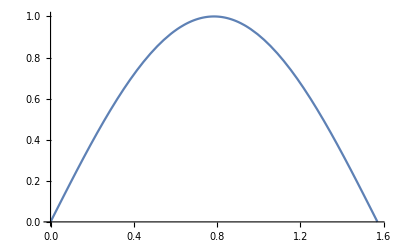

```mathematica
Plot[Sin[2 θ], {θ, 0, π/2}]
```

We note that the sine function obtains its maximum value of 1 at x = π/4rads, or 45 degrees.

Taking the distance between Caltech and PCC to be approximately equal to 1000 meters, we put R = 1000 m, and g = 9.807 ms^-2 to get:

```mathematica
R = 1000
```

1000

```mathematica
g = 9.807
```

9.807

```mathematica
V =( (R g)/Sin[2 * π/4])^0.5
```

99.0303

So, the total velocity required to reach PCC from Caltech would be approximately 9807 ms^-1, and the components would be:

```mathematica
Subscript[V, x]= V Cos[π/4]
```

70.025

```mathematica
Subscript[V, Y]=V Sin[π/4]
```

70.025

The horizontal and vertical components of velocity are the same and equal to 6934.6 ms^-1 each.

## Numeric analysis of optimum firing angle:

For two-dimensional projectile motion in absence of drag, we can define the following rules based on the differential equations:

```mathematica
eqs={x''[t]==0,y''[t]==-g}
```

{x''[t]==0,y''[t]==-9.807}

Demarcating the initial conditions, with velocity equal to 9807 ms^-1,

```mathematica
V=99.03029839397638
```

99.0303

```mathematica
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[θ], y'[0] == V Sin[θ]}
```

{x[0]==0,y[0]==0,x'[0]==99.0303 Cos[θ],y'[0]==99.0303 Sin[θ]}

```mathematica
init[A_]:=ini/.θ->A
```

```mathematica
ang= Pi/4
```

π/4

```mathematica
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]]
```

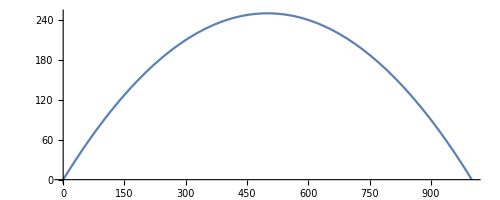

```mathematica
p1=ParametricPlot[{xx[t], yy[t]}, {t, 0, (2V Sin[ang])/g}]
```

```mathematica
ang = Pi/3
```

π/3

```mathematica
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]]
```

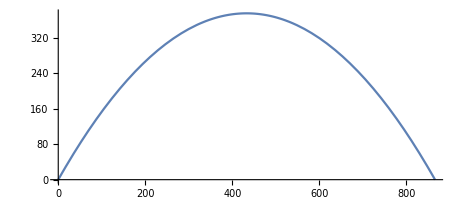

```mathematica
p2=ParametricPlot[{xx[t], yy[t]}, {t, 0, (2V Sin[ang])/g}]
```

```mathematica
ang = Pi/6
```

π/6

```mathematica
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]]
```

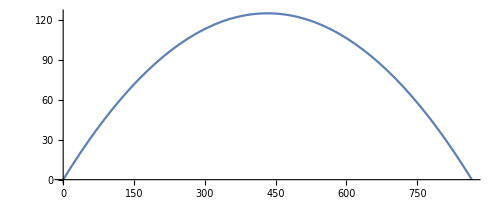

```mathematica
p3=ParametricPlot[{xx[t], yy[t]}, {t, 0, (2V Sin[ang])/g}]
```

```mathematica
Manipulate[ParametricPlot[{x[t]/.NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}][[1]], y[t]/.NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}][[1]]}, {t, 0, (2V Sin[ang])/g}],{ang, 0.00001, Pi/2}]
```

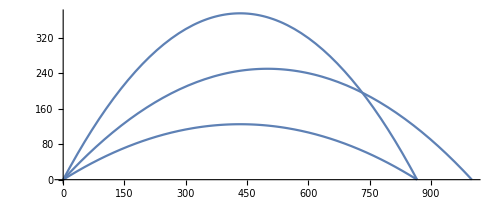

```mathematica
Show[p1,p2,p3, PlotRange->All]
```

The range is observed to be maximum for the angle of 45 degrees.

## Computation considering effects of drag:

We describe the characteristics of the grapefruit and the drag coefficients as follows:

```mathematica
m=0.5; r=0.05; d=1.3
```

1.3

```mathematica
v = (x'[t]^2+y'[t]^2)^0.5
```

(x'[t]^2+y'[t]^2)^0.5

```mathematica
Subscript[F, drag]=-0.5d r^2 v^2
```

-0.001625 (x'[t]^2+y'[t]^2)^1.

```mathematica
eqs={x''[t]==-(Abs[Subscript[F, drag]]x'[t])/(m v),y''[t]==-g-(Abs[Subscript[F, drag]]y'[t])/(m v)}
```

{x''[t]==-(0.00325 Abs[x'[t]^2+y'[t]^2]^1. x'[t])/((x'[t]^2+y'[t]^2)^0.5),y''[t]==-9.807-(0.00325 Abs[x'[t]^2+y'[t]^2]^1. y'[t])/((x'[t]^2+y'[t]^2)^0.5)}

```mathematica
ang= Pi/4
```

π/4

```mathematica
V = 99.03029839397638
```

99.0303

```mathematica
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[Pi/4], y'[0] == V Sin[Pi/4]}
```

{x[0]==0,y[0]==0,x'[0]==70.025,y'[0]==70.025}

```mathematica
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]]
```

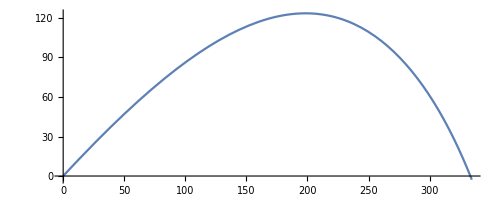

```mathematica
ParametricPlot[{xx[t], yy[t]}, {t, 0, 10}]
```

## Approximation of optimal firing angle under drag:

We define the system conditions as follows:

```mathematica
m=0.5; r=0.05; d=1.3;
v = (x'[t]^2+y'[t]^2)^0.5;
Subscript[F, drag]=-0.5d r^2 v^2
```

-0.001625 (x'[t]^2+y'[t]^2)^1.

```mathematica
eqs={x''[t]==-(Abs[Subscript[F, drag]]x'[t])/(m v),y''[t]==-g-(Abs[Subscript[F, drag]]y'[t])/(m v)}
```

{x''[t]==-(0.00325 Abs[x'[t]^2+y'[t]^2]^1. x'[t])/((x'[t]^2+y'[t]^2)^0.5),y''[t]==-9.807-(0.00325 Abs[x'[t]^2+y'[t]^2]^1. y'[t])/((x'[t]^2+y'[t]^2)^0.5)}

```mathematica
ang=Pi/4; V=100
```

100

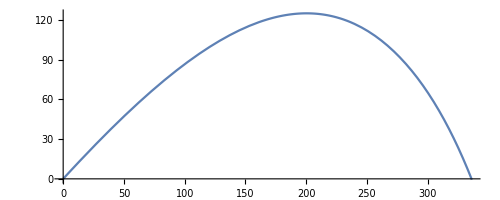

```mathematica
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p1=ParametricPlot[{xx[t], yy[t]}, {t, 0, 10}]
```

```mathematica
ang=Pi/3; V=100
```

100

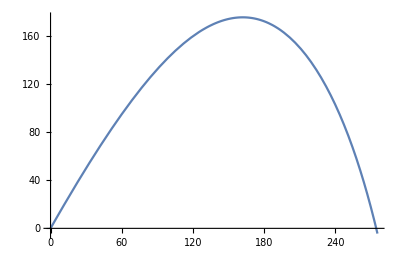

```mathematica
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p2=ParametricPlot[{xx[t], yy[t]}, {t, 0, 12}]
```

```mathematica
ang=Pi/6; V=100
```

100

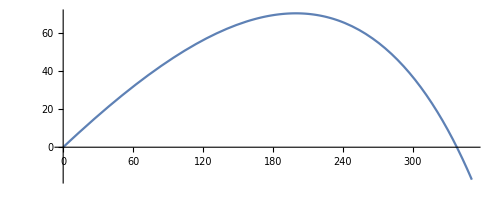

```mathematica
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p3=ParametricPlot[{xx[t], yy[t]}, {t, 0, 8}]
```

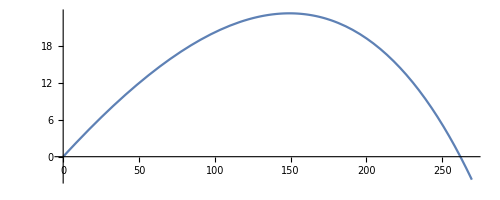

```mathematica
ang=Pi/12; V=100;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p4=ParametricPlot[{xx[t], yy[t]}, {t, 0, 4.5}]
```

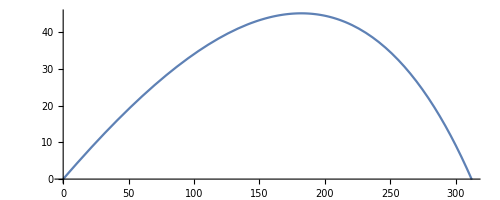

```mathematica
ang=Pi/8; V=100;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p5=ParametricPlot[{xx[t], yy[t]}, {t, 0, 6}]
```

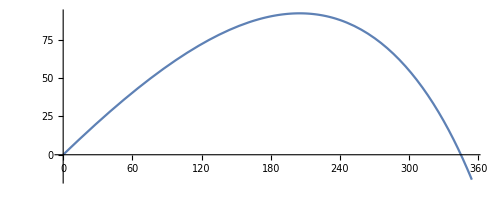

```mathematica
ang=Pi/5; V=100;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p6=ParametricPlot[{xx[t], yy[t]}, {t, 0, 9}]
```

Comparing all the cases on the same scale, we have:

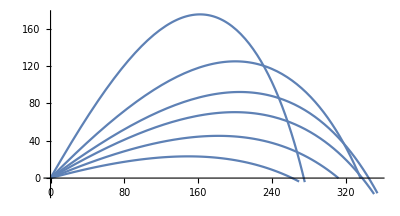

```mathematica
Show[p1,p2,p3, p4,p5,p6, PlotRange->All]
```

Note that, among the six cases, the range is maximum at the angle of π/5radians.

For getting the range of one kilometer, we need to increase the initial velocity:

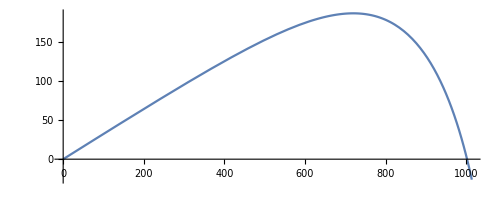

```mathematica
ang=Pi/10; V=800;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p1=ParametricPlot[{xx[t], yy[t]}, {t, 0, 12}]
```

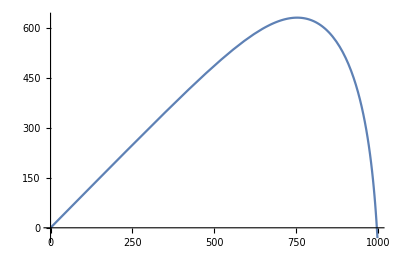

```mathematica
ang=Pi/4; V=1300;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p2=ParametricPlot[{xx[t], yy[t]}, {t, 0, 23}]
```

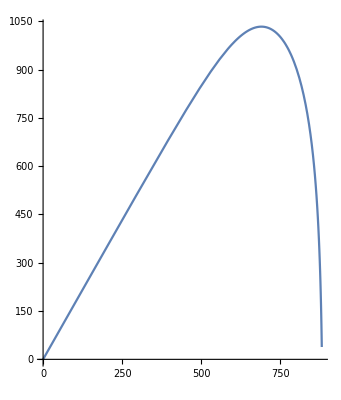

```mathematica
ang=Pi/3; V=3000;
ini = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
p3=ParametricPlot[{xx[t], yy[t]}, {t, 0, 30}]
```

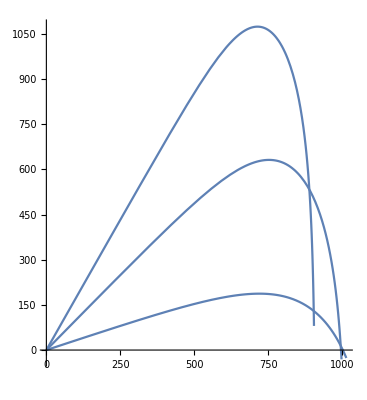

```mathematica
Show[p1,p2,p3, PlotRange->All]
```

## Direct computation of optimal firing angle under drag effects:

Define function FlightTime[] which returns the time in seconds for passed particular values of initial angle and speed.

```mathematica
FlightTime[vel_,Th_]:= 
Module[{V=vel,ang=Th},
eqs={x''[t]==-(Abs[Subscript[F, drag]]x'[t])/(m v),y''[t]==-g-(Abs[Subscript[F, drag]]y'[t])/(m v)};
init = {x[0]==0, y[0] == 0, x'[0]==V Cos[ang], y'[0] == V Sin[ang]};
rules= NDSolve[Join[eqs,init[ang]],{x,y},{t,0,(2 V)/g}];
xx[t_]:=x[t]/.rules[[1]];
yy[t_]:=y[t]/.rules[[1]];
A= Solve[yy[T]==0, T, Reals];
A[2]
]
```

```mathematica
FlightTime[100, 1]
```

Join::heads: Heads List and {x[0]==0,y[0]==0,x'[0]==100 Cos[1],y'[0]==100 Sin[1]} at positions 1 and 2 are expected to be the same.

NDSolve::deqn: Equation or list of equations expected instead of Join[{x''[t]==-(Abs[F_drag] x'[t])/(m v),y''[t]==-g-(Abs[F_drag] y'[t])/(m v)},{x[0]==0,y[0]==0,x'[0]==100 Cos[1],y'[0]==100 Sin[1]}[1]] in the first argument Join[{x''[t]==-(Abs[F_drag] x'[t])/(m v),y''[t]==-g-(Abs[F_drag] y'[t])/(m v)},{x[0]==0,y[0]==0,x'[0]==100 Cos[1],y'[0]==100 Sin[1]}[1]].

ReplaceAll::reps: {Join[{x''[t]==-(Abs[F_drag] x'[t])/(m v),y''[t]==-g-(Abs[Subscript[«2»]] y'[t])/(m v)},{x[0]==0,y[0]==0,x'[0]==100 Cos[1],y'[0]==100 Sin[1]}[1]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(y[T]/.Join[{x''[t]==-(Abs[F_drag] x'[t])/(m v),y''[t]==-g-(Abs[F_drag] y'[t])/(m v)},{x[0]==0,y[0]==0,x'[0]==100 Cos[1],y'[0]==100 Sin[1]}[1]])==0,T,ℝ][2]

```mathematica
RangeTime[vel_,Th_]:=
Module[{V=vel,ang=Th},
time = FlightTime[V, ang];
List[xx[time], time]
]
```

```mathematica
IniVel[Th_, R_]:=
Module[{ang=Th, ran=R, vel=1, diff=0, min_diff=1},
While[{diff<=min_diff}, 
min_diff=diff;
vel=vel +10; 
diff=ran-RangeTime[vel,ang]];
vel
]
```

```mathematica
least[R_]:=
Module[{ran=R, ang=0, min_vel=10^10, vel=1},
while [{vel<=min_vel}, min_vel=vel;
ang=ang +0.1; 
vel=IniVel[ang, ran]];
List[vel, ang]
]
```